# Documentation of “cDMRG_input”

## Constructing basis functions

As detailed in the supplement, we build our local basis out of symmetrized monomials written as {p_1,p_2,..., p_n}=x_1^p_1 x_2^p_2... x_n^p_n when x_1<x_2<...<x_n.  Otherwise we permute.  We work on the domain [0,1], then later rescale.  These choices are made so that the overlaps are quick to calculate.  Note, the monomials are non-orthogonal.

## Building monomials

Generate all monomials with maximum degree d_max, i.e.,  p_1+p_2+...+p_n<=d_max.

```mathematica
(*All n-variable monomials with degree d*)
allmonomialsfixedorder[n_Integer,d_Integer]:=Block[{part=IntegerPartitions[d+n,{n}]},Flatten[Permutations/@(part-1),1]];
(*All n-variable monomials with maximum degree Subscript[d, max]*)
allmonomials[n_Integer,dmax_Integer]:=Join@@Table[allmonomialsfixedorder[n,d],{d,0,dmax}];
```

```mathematica
allmonomials[3,2]
```

{{0,0,0},{1,0,0},{0,1,0},{0,0,1},{2,0,0},{0,2,0},{0,0,2},{1,1,0},{1,0,1},{0,1,1}}

We won’t need it very often, but here is the recipe for making the monomials  (Remember these are only for x[0]<x[1]<x[2]).

```mathematica
tupletomonomial[mon_]:=Times@@(Array[x,Length[mon]]^mon)
```

```mathematica
tupletomonomial/@allmonomials[3,2]
```

{1,x[1],x[2],x[3],x[1]^2,x[2]^2,x[3]^2,x[1] x[2],x[1] x[3],x[2] x[3]}

## Overlaps

Routine to calculate the integral of a symmetrized monomial (up to n!), defined as ℐ(p) in the supplement [Eq. (S15)].  We will need this for calculating overlaps.
monint[{p_1,p_2,..., p_n}] = ∫_0^1 dx_n∫_0^x_n dx_(n-1)...∫_0^x_2 dx_1 x_1^p_1 x_2^p_2... x_n^p_n.

```mathematica
monint=Compile[{{mon,_Real,1}},1./Times@@Accumulate[mon+1.],"RuntimeOptions"->"Speed","CompilationTarget"->"C"]
```

CompiledFunction[…]

Here is integrating a 30-particle state {1,1,...,1}, for which the integral should be  monint[{1,1,...,1}] = 1/(n! 2^n).

```mathematica
{monint@Table[1,{30}]//AbsoluteTiming,0.5^30/30!}
```

{{0.000019,3.51107×10^-42},3.51107×10^-42}

We can benefit from storing these integrals.

```mathematica
Clear[fmonint];
fmonint[mon_]:=fmonint[mon]=monint[mon];
```

The inner product of two monomials p and q is given by monint[p+q].  This is symmetric in p and q.  Thus, to calculate the matrix of inner products between all monomials, we only compute the lower-triangular matrix and then symmetrize.

```mathematica
(*Create a symmetrix matrix from the lower half*)
makesym[lower_]:=MapThread[Join,{lower,Rest/@Flatten[lower,{{2},{1}}]}];
(*a symmetric version of "Outer" that generates the lower-half matrix and symmetrizes*)
symOuter[f_,list_]:=makesym@Table[f[list[[i]],list[[j]]],{i,Length[list]},{j,i}];
```

Here is an example for n=3 particles and maximum monomial degree d_max=2.

```mathematica
monlist=allmonomials[3,2];
3!*symOuter[fmonint[#1+#2]&,monlist]//MatrixForm
```

(1. | 0.25 | 0.5 | 0.75 | 0.1 | 0.3 | 0.6 | 0.15 | 0.2 | 0.4
0.25 | 0.1 | 0.15 | 0.2 | 0.05 | 0.1 | 0.166667 | 0.0666667 | 0.0833333 | 0.125
0.5 | 0.15 | 0.3 | 0.4 | 0.0666667 | 0.2 | 0.333333 | 0.1 | 0.125 | 0.25
0.75 | 0.2 | 0.4 | 0.6 | 0.0833333 | 0.25 | 0.5 | 0.125 | 0.166667 | 0.333333
0.1 | 0.05 | 0.0666667 | 0.0833333 | 0.0285714 | 0.047619 | 0.0714286 | 0.0357143 | 0.0428571 | 0.0571429
0.3 | 0.1 | 0.2 | 0.25 | 0.047619 | 0.142857 | 0.214286 | 0.0714286 | 0.0857143 | 0.171429
0.6 | 0.166667 | 0.333333 | 0.5 | 0.0714286 | 0.214286 | 0.428571 | 0.107143 | 0.142857 | 0.285714
0.15 | 0.0666667 | 0.1 | 0.125 | 0.0357143 | 0.0714286 | 0.107143 | 0.047619 | 0.0571429 | 0.0857143
0.2 | 0.0833333 | 0.125 | 0.166667 | 0.0428571 | 0.0857143 | 0.142857 | 0.0571429 | 0.0714286 | 0.107143
0.4 | 0.125 | 0.25 | 0.333333 | 0.0571429 | 0.171429 | 0.285714 | 0.0857143 | 0.107143 | 0.214286)

Sample computation time for n=10 and d_max=3.

```mathematica
monlist=allmonomials[10,3];
AbsoluteTiming[symOuter[fmonint[#1+#2]&,monlist];]
```

{0.158504,Null}

## Legendre kinetic energy

As explained in Sec. SII C, n-body Legendre polynomials are generated by the eigenvalue equation K_L ψ=ℰ ψ, where  K_L is an effective kinetic energy

K_L=-(1/2)∑_(i=1)^n ∂_x_i[x_i(1-x_i) ∂_x_i ].

We write K_L as a matrix in the space of monomials.  The matrix elements are given in Eq. (S43) of the supplement.  Below is a routine to calculate these (up to n!/2).  Note that “incr(p,i,s)” increments the i-th element of p by s.

```mathematica
legendreKE=
Compile[{{mon1,_Real,1},{mon2,_Real,1}},
Block[{sum=mon1+mon2,prod=mon1*mon2,res=0.},
Do[If[prod[[i]]!=0,res+=prod[[i]]*monint@MapAt[#-1&,sum,i]],{i,Length[prod]}]; (*∑_i Subscript[p, i] Subscript[q, i] ℐ(incr(p+q,i,-1))*)
res-Total[prod]*monint[sum]], (*subtract ∑_i Subscript[p, i] Subscript[q, i] ℐ(p+q)*)
"CompilationTarget"->"C","RuntimeOptions"->"Speed"]
```

CompiledFunction[…]

Since K_L is symmetric in the two monomials, we use the symmetric version of “Outer” defined above to calculate the full matrix. Below is an example for n=3 and d_max=2.

```mathematica
monlist=allmonomials[3,2];
symOuter[legendreKE,monlist]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.025 | 0. | 0. | 0.0166667 | 0. | 0. | 0.0138889 | 0.0194444 | 0.
0. | 0. | 0.0333333 | 0. | 0. | 0.0333333 | 0. | 0.00833333 | 0. | 0.025
0. | 0. | 0. | 0.025 | 0. | 0. | 0.0333333 | 0. | 0.00555556 | 0.0111111
0. | 0.0166667 | 0. | 0. | 0.0142857 | 0. | 0. | 0.0103175 | 0.0134921 | 0.
0. | 0. | 0.0333333 | 0. | 0. | 0.0380952 | 0. | 0.00952381 | 0. | 0.0261905
0. | 0. | 0. | 0.0333333 | 0. | 0. | 0.047619 | 0. | 0.00793651 | 0.015873
0. | 0.0138889 | 0.00833333 | 0. | 0.0103175 | 0.00952381 | 0. | 0.0119048 | 0.0113095 | 0.00654762
0. | 0.0194444 | 0. | 0.00555556 | 0.0134921 | 0. | 0.00793651 | 0.0113095 | 0.0178571 | 0.00297619
0. | 0. | 0.025 | 0.0111111 | 0. | 0.0261905 | 0.015873 | 0.00654762 | 0.00297619 | 0.0257937)

Sample computation time for n=10 and d_max=3.

```mathematica
monlist=allmonomials[10,3];
AbsoluteTiming[symOuter[legendreKE,monlist];]
```

{0.134953,Null}

## Legendre interaction energy

To encode the physics of contact interactions, we want to generalize the Legendre polynomials to include cusps when two particles touch.  As explained in Sec. SII C of the supplement, this can be done by changing the eigenvalue equation to  (K_L+c U_L)ψ=ℰ ψ, where  U_L is an effective interaction energy

U_L=∑_(i<j) x_i(1-x_i)δ(x_i-x_j).

The matrix element of  U_L between the monomials are given by Eq. (S44). Below is a routine to calculate these (up to n!/2).

```mathematica
(*Auxiliary function to merge the i-th and (i+1)-th elements of a monomial*)
merge=Compile[{{mon,_Integer,1},{i,_Integer}},Join[Take[mon,i-1],{mon[[i]]+mon[[i+1]]},Drop[mon,i+1]]];
(*Main function*)
legendreIE=
Compile[{{sum,_Integer,1}},
Block[{merged,res=0.},
Do[
merged=merge[sum,i]; (*merge(p+q,i)*)
res+=monint@MapAt[#+1&,merged,i]-monint@MapAt[#+2&,merged,i];, (*∑_i ℐ(incr(merge(p+q,i),i,1))-ℐ(incr(merge(p+q,i),i,2))*)
{i,Length[sum]-1}];
res],"CompilationTarget"->"C","RuntimeOptions"->"Speed"]
```

CompiledFunction[…]

We can benefit from storing these integrals.

```mathematica
Clear[flegendreIE];
flegendreIE[sum_]:=flegendreIE[sum]=legendreIE[sum]
```

Here is an example for n=3 and d_max=2.  We again use the symmetric version of “Outer” to calculate the symmetric matrix.

```mathematica
monlist=allmonomials[3,2];
symOuter[flegendreIE[#1+#2]&,monlist]//MatrixForm
```

(0.166667 | 0.0583333 | 0.0833333 | 0.108333 | 0.0277778 | 0.05 | 0.0777778 | 0.0333333 | 0.0416667 | 0.0583333
0.0583333 | 0.0277778 | 0.0333333 | 0.0416667 | 0.0154762 | 0.0214286 | 0.031746 | 0.0174603 | 0.0210317 | 0.025
0.0833333 | 0.0333333 | 0.05 | 0.0583333 | 0.0174603 | 0.0333333 | 0.0436508 | 0.0214286 | 0.025 | 0.0369048
0.108333 | 0.0416667 | 0.0583333 | 0.0777778 | 0.0210317 | 0.0369048 | 0.0595238 | 0.025 | 0.031746 | 0.0436508
0.0277778 | 0.0154762 | 0.0174603 | 0.0210317 | 0.00952381 | 0.0119048 | 0.0166667 | 0.0104167 | 0.0122024 | 0.0136905
0.05 | 0.0214286 | 0.0333333 | 0.0369048 | 0.0119048 | 0.0238095 | 0.0285714 | 0.014881 | 0.0166667 | 0.0255952
0.0777778 | 0.031746 | 0.0436508 | 0.0595238 | 0.0166667 | 0.0285714 | 0.047619 | 0.0196429 | 0.0252976 | 0.0342262
0.0333333 | 0.0174603 | 0.0214286 | 0.025 | 0.0104167 | 0.014881 | 0.0196429 | 0.0119048 | 0.0136905 | 0.0166667
0.0416667 | 0.0210317 | 0.025 | 0.031746 | 0.0122024 | 0.0166667 | 0.0252976 | 0.0136905 | 0.0166667 | 0.0196429
0.0583333 | 0.025 | 0.0369048 | 0.0436508 | 0.0136905 | 0.0255952 | 0.0342262 | 0.0166667 | 0.0196429 | 0.0285714)

Sample computation time for n=10 and d_max=3.

```mathematica
monlist=allmonomials[10,3];
AbsoluteTiming[symOuter[flegendreIE[#1+#2]&,monlist];]
```

{0.227456,Null}

## Making the basis

As the monomials are non-orthogonal, we solve the generalized eigenvalue problem (K_L+c U_L)A=ℰ O A, where  A  gives the basis coefficients in the monomials and  O is matrix of overlaps between the monomials -- see Sec. SII C of the supplement.

```mathematica
legendrebasis[n_Integer,dmax_Integer,c_?NumericQ,keep_:Infinity(*max number of basis functions to be kept*)]:=
If[n==0,{{1.}}, (*vacuum state*)
Block[{monlist=allmonomials[n,dmax],ov,kin,int,akeep,eigenvecs,scale=n!},
ov=symOuter[fmonint[#1+#2]&,monlist]; (*overlaps between the monomials*)
kin=symOuter[legendreKE,monlist]; (*matrix of kinetic energy Subscript[K, L]*)
int=symOuter[flegendreIE[#1+#2]&,monlist]; (*matrix of interaction energy Subscript[U, L]*)
akeep=Min[Length[monlist],keep]; (*actual number of basis functions retained*)
eigenvecs=Reverse@Eigenvectors[{kin+c*int ,ov},-akeep]; (*basis vectors sorted by increasing energy*)
#/Sqrt[scale*(#.ov.#)]&/@eigenvecs]] (*normalized basis vectors*)
```

Sample calculation for n=2,d_max=3,c=5,  where the 3 lowest-energy basis states are kept.

```mathematica
es=legendrebasis[2,3,c=5,3]
```

{{-0.641933,1.61478,-1.28678,0.417775,0.574007,-1.31978,0.240943,-0.240943,-0.566597,0.566597},{-1.98015,6.76866,-1.21528,-3.27117,4.71278,-6.22083,-1.51734,-1.51734,3.11042,3.11042},{2.262,-8.12016,-0.141081,4.40294,-8.28823,12.1465,-2.64657,2.64657,-4.75146,4.75146}}

Check that the basis states have the expected cusp when two particles touch.

```mathematica
gs[x_,y_]=-es[[1]].(tupletomonomial/@allmonomials[2,3])/.{x[1]->Min[x,y],x[2]->Max[x,y]}
```

0.641933+1.28678 Max[x,y]-0.574007 Max[x,y]^2+0.240943 Max[x,y]^3-1.61478 Min[x,y]+1.31978 Max[x,y] Min[x,y]-0.566597 Max[x,y]^2 Min[x,y]-0.417775 Min[x,y]^2+0.566597 Max[x,y] Min[x,y]^2-0.240943 Min[x,y]^3

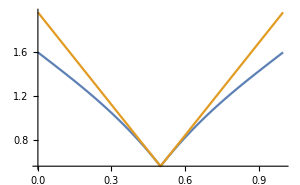
{-Graphics3D-,-Graphics-}

```mathematica
{Plot3D[gs[x,y],{x,0,1},{y,0,1},ImageSize->300],
Plot[{gs[x,1-x],(1+c*Abs[x-1/2])*gs[1/2,1/2]},{x,0,1},ImageSize->300]}
```

```mathematica
Clear[c]
```

Sample computation time for n=10 and d_max=3.

```mathematica
Clear[fmonint];(*clear stored values to get a more accurate estimate of the time*)
fmonint[mon_]:=fmonint[mon]=monint[mon];
Clear[flegendreIE];
flegendreIE[sum_]:=flegendreIE[sum]=legendreIE[sum];
```

```mathematica
legendrebasis[10,3,1,3];//AbsoluteTiming
```

{0.521304,Null}

## Local operator blocks

We calculate the action of the local operators on the monomials. These are later transformed to the actual basis using the basis vectors found above.

## Kinetic energy

The matrix elements of the kinetic energy,  ,,⟨ψ_1|K|ψ_2⟩=(1/2)∫_0^1 dx_1∫_0^1 dx_2...∫_0^1 dx_n ∇ψ_1.∇ψ_2,  between two monomials are given by Eq. (S33) in the supplement.  Below is a routine to calculate these (up to n!/2).  As before, “incr(p,i,s)” increments the i-th element of p by s.

```mathematica
KE=
Compile[{{mon1,_Real,1},{mon2,_Real,1}},
Block[{sum=mon1+mon2,prod=mon1*mon2,res=0.},
Do[If[prod[[i]]!=0,res+=prod[[i]]*monint@MapAt[#-2&,sum,i]],{i,Length[prod]}]; (*∑_i Subscript[p, i] Subscript[q, i] ℐ(incr(p+q,i,-2))*)
res],
"CompilationTarget"->"C","RuntimeOptions"->"Speed"]
```

CompiledFunction[…]

We generate the matrix by using a symmetric version of “Outer” defined above.

```mathematica
kinoverlaps[n_Integer,dmax_Integer]:=Block[{monlist=allmonomials[n,dmax]},(n!/2)*symOuter[KE,monlist]];
```

Here is an example for n=3 and d_max=2.

```mathematica
kinoverlaps[3,2]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.5 | 0. | 0. | 0.25 | 0. | 0. | 0.25 | 0.375 | 0.
0. | 0. | 0.5 | 0. | 0. | 0.5 | 0. | 0.125 | 0. | 0.375
0. | 0. | 0. | 0.5 | 0. | 0. | 0.75 | 0. | 0.125 | 0.25
0. | 0.25 | 0. | 0. | 0.2 | 0. | 0. | 0.15 | 0.2 | 0.
0. | 0. | 0.5 | 0. | 0. | 0.6 | 0. | 0.15 | 0. | 0.4
0. | 0. | 0. | 0.75 | 0. | 0. | 1.2 | 0. | 0.2 | 0.4
0. | 0.25 | 0.125 | 0. | 0.15 | 0.15 | 0. | 0.2 | 0.2 | 0.1
0. | 0.375 | 0. | 0.125 | 0.2 | 0. | 0.2 | 0.2 | 0.35 | 0.075
0. | 0. | 0.375 | 0.25 | 0. | 0.4 | 0.4 | 0.1 | 0.075 | 0.45)

Sample computation time for n=10 and d_max=3.

```mathematica
kinoverlaps[10,3];//AbsoluteTiming
```

{0.12623,Null}

## Interaction energy

Matrix elements of the contact interaction U_L=∑_(i<j) δ(x_i-x_j)  between monomials are given by Eq. (S37) of the supplement.  Below we calculate these up to n!/2.  Note that “merge” is defined above.

```mathematica
IE=
Compile[{{sum,_Integer,1}},
Block[{merged,res=0.},
Do[
merged=merge[sum,i]; (*merge the i-th and (i+1)-th elements*)
res+=monint@merged;,
{i,Length[sum]-1}];
res],
"CompilationTarget"->"C","RuntimeOptions"->"Speed"]
```

CompiledFunction[…]

We can benefit from storing these integrals.

```mathematica
Clear[fIE];
fIE[sum_]:=fIE[sum]=IE[sum]
```

Below is a routine for generating the full symmetric matrix.

```mathematica
intoverlaps[n_Integer,dmax_Integer]:=Block[{monlist=allmonomials[n,dmax]},(n!/2)*symOuter[fIE[#1+#2]&,monlist]];
```

Here is an example for n=3 and d_max=2.

```mathematica
intoverlaps[3,2]//MatrixForm
```

(3. | 1. | 1.5 | 2. | 0.5 | 1. | 1.5 | 0.625 | 0.75 | 1.125
1. | 0.5 | 0.625 | 0.75 | 0.3 | 0.45 | 0.6 | 0.35 | 0.4 | 0.5
1.5 | 0.625 | 1. | 1.125 | 0.35 | 0.75 | 0.9 | 0.45 | 0.5 | 0.8
2. | 0.75 | 1.125 | 1.5 | 0.4 | 0.8 | 1.2 | 0.5 | 0.6 | 0.9
0.5 | 0.3 | 0.35 | 0.4 | 0.2 | 0.266667 | 0.333333 | 0.225 | 0.25 | 0.291667
1. | 0.45 | 0.75 | 0.8 | 0.266667 | 0.6 | 0.666667 | 0.35 | 0.375 | 0.625
1.5 | 0.6 | 0.9 | 1.2 | 0.333333 | 0.666667 | 1. | 0.416667 | 0.5 | 0.75
0.625 | 0.35 | 0.45 | 0.5 | 0.225 | 0.35 | 0.416667 | 0.266667 | 0.291667 | 0.375
0.75 | 0.4 | 0.5 | 0.6 | 0.25 | 0.375 | 0.5 | 0.291667 | 0.333333 | 0.416667
1.125 | 0.5 | 0.8 | 0.9 | 0.291667 | 0.625 | 0.75 | 0.375 | 0.416667 | 0.666667)

Sample computation time for n=10 and d_max=3.

```mathematica
intoverlaps[10,3];//AbsoluteTiming
```

{0.217729,Null}

## Density

To calculate the density and density-density correlations, we store the density operator ρ(x) in the local basis.  As derived in Eq. (S28) of the supplement, the matrix elements are polynomials in x.  Below is a routine to calculate these polynomial coefficients between two monomials, which depend only on their sum p+q.

```mathematica
denscoefs=
Compile[{{sum,_Integer,1}},
Block[{n=Length[sum],powers,coefs,phases,leftint,rightint,middleint,partialsums={-1.},result,scale},
powers=Accumulate[Join[{sum[[1]]},Rest[sum]+1]]; (*powers of x with nonzero coefficients*)
result=ConstantArray[0.,1+powers[[-1]]]; (*list of coefficients to be updated*)
phases=(-1.)^Range[n]; (*signs originating from the definite integrals -- see Eq.(S23)*)
leftint=phases*Join[{1.},Table[monint@Take[sum,i],{i,n-1}]]; (*integrating over all particles to the left -- Subscript[ℐ, l] in Eq.(S28)*)
rightint=phases*Join[Table[monint@Drop[sum,j],{j,n-1}],{1.}]; (*part of Subscript[ℐ, r] in Eq.(S28) that is independent of x -- see Eq.(S23)*)
Do[
AppendTo[partialsums,Sum[leftint[[i]]*monint[Take[sum,{j,i+1,-1}]],{i,j-1}]+leftint[[j]]];, (*nonzero coefficients of different powers of x originating from Subscript[ℐ, r] in Eq.(S28) -- see Eq.(S23)*)
{j,2,n}];
coefs=partialsums*rightint; (*multiply by the x-independent part*)
scale=N@n!; (*symmetrization factor*)
Do[result[[1+powers[[i]]]]=scale*coefs[[i]],{i,n}]; (*update the nonzero coefficients*)
result
],"RuntimeOptions"->"Speed","CompilationTarget"->"C"]
```

CompiledFunction[…]

Here is integrating a 22-particle state {1,1,...,1}, for which the integral should be  x n/2^(n-1).

```mathematica
{22/2^21.,denscoefs@Table[1,{22}]//AbsoluteTiming}
```

{0.0000104904,{0.000179,{0.,0.0000104904,0.,0.,0.,0.,0.,2.32352×10^-18,0.,1.04558×10^-17,0.,4.44373×10^-17,0.,-8.88745×10^-17,0.,3.3328×10^-16,0.,2.15798×10^-14,0.,1.70597×10^-14,0.,1.79127×10^-13,0.,1.75929×10^-14,0.,-6.30411×10^-13,0.,2.23003×10^-13,0.,2.23347×10^-15,0.,5.40435×10^-14,0.,-9.60888×10^-14,0.,-2.06292×10^-14,0.,-1.84643×10^-13,0.,3.05499×10^-15,0.,-5.92785×10^-16,0.,-1.69231×10^-16}}}

We can benefit from storing these coefficients.

```mathematica
Clear[fdenscoefs];
fdenscoefs[sum_]:=fdenscoefs[sum]=denscoefs[sum]
```

Below is a routine for generating the full symmetric matrix.

```mathematica
densoverlaps[n_Integer,dmax_Integer]:=If[n==0,{{{}}},Block[{monlist=allmonomials[n,dmax]},symOuter[fdenscoefs[#1+#2]&,monlist]]];
```

Here is an example for n=3 and d_max=1.

```mathematica
densoverlaps[3,1]//MatrixForm
```

({3.,0.,0.} | {0.,3.,-3.,1.} | {1.,0.,3.,-2.} | {2.,0.,0.,1.}
{0.,3.,-3.,1.} | {0.,0.,3.,-4.,1.5} | {0.,1.,0.,0.,-0.25} | {0.,2.,-1.5,0.,0.5}
{1.,0.,3.,-2.} | {0.,1.,0.,0.,-0.25} | {0.5,0.,0.,4.,-3.} | {0.75,0.,1.5,0.,-0.25}
{2.,0.,0.,1.} | {0.,2.,-1.5,0.,0.5} | {0.75,0.,1.5,0.,-0.25} | {1.5,0.,0.,0.,1.5})

Sample computation time for n=10 and d_max=3.

```mathematica
densoverlaps[10,3];//AbsoluteTiming
```

{0.44628,Null}

We can convert these coefficients back to polynomials using the function below.

```mathematica
poly[coefs_?VectorQ,x_]:=coefs.x^Range[0,Length@coefs-1];
poly[coefs_?VectorQ,0]:=If[coefs!={},coefs[[1]],0];
poly[table_/;MatrixQ[table,VectorQ],x_]:=Map[poly[#,x]&,table,{2}];
```

```mathematica
poly[densoverlaps[3,1],x]//MatrixForm
```

(3. | 0.+3. x-3. x^2+1. x^3 | 1.+3. x^2-2. x^3 | 2.+1. x^3
0.+3. x-3. x^2+1. x^3 | 0.+3. x^2-4. x^3+1.5 x^4 | 0.+1. x-0.25 x^4 | 0.+2. x-1.5 x^2+0.5 x^4
1.+3. x^2-2. x^3 | 0.+1. x-0.25 x^4 | 0.5+4. x^3-3. x^4 | 0.75+1.5 x^2-0.25 x^4
2.+1. x^3 | 0.+2. x-1.5 x^2+0.5 x^4 | 0.75+1.5 x^2-0.25 x^4 | 1.5+1.5 x^4)

## Field operator

To calculate the single-particle correlations and the discontinuity, we store the field operator in the local basis.  As derived in Eq. (S21) of the supplement, the matrix elements are polynomials in x.  Below is a routine to calculate these polynomial coefficients between two monomials of size n-1 and n.

```mathematica
psicoefs=
Compile[{{smallmon,_Integer,1},{bigmon,_Integer,1}},(*smallermon has size n-1, biggermon has size n*)
Block[{suml=smallmon+Most[bigmon],sumr=smallmon+Rest[bigmon],n=Length[bigmon],powers,coefs,phases,leftint,rightint,middleint,partialsums={-1.},result,scale},
powers=Accumulate[Join[{bigmon[[1]]},sumr+1]]; (*powers of x with nonzero coefficients*)
result=ConstantArray[0.,1+powers[[-1]]]; (*list of coefficients to be updated*)
phases=(-1.)^Range[n]; (*signs originating from the definite integrals -- see Eq.(S23)*)
leftint=phases*Join[{1.},Table[monint@Take[suml,i],{i,n-1}]]; (*integrating over all particles to the left -- Subscript[ℐ, l] in Eq.(S21)*)
rightint=phases*Join[Table[monint@Drop[sumr,j],{j,0,n-2}],{1.}]; (*x-independent part of Subscript[ℐ, r] in Eq.(S21) -- see Eq.(S23)*)
Do[
AppendTo[partialsums,Sum[leftint[[i]]*monint[Take[sumr,{j,i,-1}]],{i,j}]+leftint[[j+1]]];,(*nonzero coefficients of different powers of x originating from Subscript[ℐ, r] in Eq.(S21) -- see Eq.(S23)*)
{j,n-1}];
coefs=partialsums*rightint; (*multiply by the x-independent part*)
scale=Sqrt[N@n]*Gamma[N@n]; (*symmetrization factor*)
Do[result[[1+powers[[i]]]]=scale*coefs[[i]],{i,n}]; (*update the nonzero coefficients*)
result
],"RuntimeOptions"->"Speed","CompilationTarget"->"C"]
```

CompiledFunction[…]

Here is an integral between a flat 21-particle state {0,0,...,0} and a linear 22-particle state {1,1,...,1}, for which the result should be  x Sqrt[n]/2^(n-1).

```mathematica
{Sqrt[22]/2^21.,psicoefs[Table[0,21],Table[1,{22}]]//AbsoluteTiming}
```

{2.23656×10^-6,{0.000177,{0.,2.23656×10^-6,0.,0.,0.,0.,0.,4.95376×10^-19,0.,2.22919×10^-18,0.,9.47406×10^-18,0.,-1.89481×10^-17,0.,7.10554×10^-17,0.,4.60084×10^-15,0.,3.63715×10^-15,0.,3.81901×10^-14,0.,3.75081×10^-15,0.,-1.34404×10^-13,0.,4.75445×10^-14,0.,4.76177×10^-16,0.,1.15221×10^-14,0.,-2.04862×10^-14,0.,-4.39816×10^-15,0.,-3.93661×10^-14,0.,6.51327×10^-16,0.,-1.26382×10^-16,0.,-3.60802×10^-17}}}

Below is a routine for generating the full matrix between monomials of size n-1 and n.

```mathematica
psioverlaps[n_Integer,dmaxSmall_Integer,dmaxBig_Integer]:=
Block[{smallmons=allmonomials[n-1,dmaxSmall],bigmons=allmonomials[n,dmaxBig]},Outer[psicoefs,smallmons,bigmons,1]];
```

Here is an example for n=3 and d_max=1.

```mathematica
psioverlaps[3,1,1]//MatrixForm
```

({1.73205,0.,0.} | {0.,1.73205,-1.73205,0.57735} | {0.57735,0.,1.73205,-1.1547} | {1.1547,0.,0.,0.57735}
{0.57735,0.,0.,-9.61481×10^-17} | {0.,0.57735,0.,-0.57735,0.288675} | {0.288675,0.,0.,0.57735,-0.433013} | {0.433013,0.,0.,0.,0.144338}
{1.1547,0.,0.,-1.92296×10^-16} | {0.,1.1547,-0.866025,0.,0.144338} | {0.433013,0.,0.866025,0.,-0.433013} | {0.866025,0.,0.,0.,0.288675})

```mathematica
psioverlaps[10,3,3];//AbsoluteTiming
```

{2.25134,Null}

The field operators at the left and right boundaries can be found by converting these coefficients to polynomials in x and setting x=0 or x=1, respectively.

```mathematica
Table[MatrixForm@poly[psioverlaps[3,1,1],x],{x,{0,1}}]
```

{(1.73205 | 0. | 0.57735 | 1.1547
0.57735 | 0. | 0.288675 | 0.433013
1.1547 | 0. | 0.433013 | 0.866025),(1.73205 | 0.57735 | 1.1547 | 1.73205
0.57735 | 0.288675 | 0.433013 | 0.57735
1.1547 | 0.433013 | 0.866025 | 1.1547)}

## Potential energy

The matrix elements of the potential energy can be found by integrating the elements of the density times the potential V(x) over x.  As the density is a polynomial in x, we calculate the integer moments of V(x) over different segments.  As shown in Eq. (S30) of the supplement, for  V(x)=V_0 cos^2(k x), these are given by incomplete gamma functions.

We use a series expansion to calculate the lower incomplete gamma function, γ(p,z):=∫_0^z dt t^(p-1)e^-t=e^-z∑_(k=0)^∞ z^(p+k)/(p)_(k+1),  where  (p)_(k+1):=p(p+1)...(p+k).

```mathematica
incgamma=
Compile[{{p,_Integer},{z,_Complex}}, (*also valid for complex p with Re(p)>0*)
Block[{sum=1.+0.*I,residue,k=1.},
residue=sum;
While[Abs[residue/sum]>10^-15., (*stop when this precision is reached*)
residue*=z/(p+k);
sum+=residue;
k++];
Exp[-z]*z^p*sum/p],
"RuntimeOptions"->"Speed","CompilationTarget"->"C"]
```

CompiledFunction[…]

Mathematica’s built-in function does not compile.

```mathematica
{incgamma[20,-1.5*I]//AbsoluteTiming,Gamma[20,0,-1.5*I]//AbsoluteTiming}
```

{{0.000014,23.4976+164.206 ⅈ},{0.000047,23.4976+164.206 ⅈ}}

For density = ∑_p c_p x^p,  we calculate the potential energy PE = ∑_p 2 c_(p-1)∫_0^1 dx x^(p-1)cos^2[(a x+b)/2] =  ∑_p c_(p-1)(1/p+a^-p Re[i^k e^(i b)γ(p,-i a)]) -- see Eq. (S30).

```mathematica
PE=
Compile[{{ncoefs,_Real,1},{a,_Real},{b,_Real}},
Block[{len=Length[ncoefs],res=0.},
Do[
If[ncoefs[[p]]!=0,res+=ncoefs[[p]]*(1./p+Re[I^p*Exp[I*b]*incgamma[p,-I*a]]/a^p)],
{p,len}];
res],
"RuntimeOptions"->"Speed","CompilationTarget"->"C"]
```

CompiledFunction[…]

We need to calculate PE for a symmetric matrix of density coefficients.  Below is a routine for that.  Note that {a,b} will vary with the segment.

```mathematica
symPE[matncoefs_,{a_,b_}]:=makesym@Table[PE[matncoefs[[i,j]],a,b],{i,Length[matncoefs]},{j,i}]
```

Here is an example for monomials with n=3 and d_max=2.

```mathematica
symPE[densoverlaps[3,2],{0.1,0.3}]//MatrixForm
```

(5.81694 | 1.4517 | 2.90504 | 4.3601 | 0.579992 | 1.74163 | 3.48667 | 0.870267 | 1.16083 | 2.32304
1.4517 | 0.579992 | 0.870267 | 1.16083 | 0.289745 | 0.579814 | 0.967045 | 0.386409 | 0.483156 | 0.724975
2.90504 | 0.870267 | 1.74163 | 2.32304 | 0.386409 | 1.16042 | 1.93526 | 0.579814 | 0.724975 | 1.45089
4.3601 | 1.16083 | 2.32304 | 3.48667 | 0.483156 | 1.45089 | 2.90472 | 0.724975 | 0.967045 | 1.93526
0.579992 | 0.289745 | 0.386409 | 0.483156 | 0.16546 | 0.27587 | 0.414024 | 0.206856 | 0.248284 | 0.331117
1.74163 | 0.579814 | 1.16042 | 1.45089 | 0.27587 | 0.828506 | 1.24332 | 0.413956 | 0.496852 | 0.994396
3.48667 | 0.967045 | 1.93526 | 2.90472 | 0.414024 | 1.24332 | 2.48921 | 0.621247 | 0.82869 | 1.65841
0.870267 | 0.386409 | 0.579814 | 0.724975 | 0.206856 | 0.413956 | 0.621247 | 0.27587 | 0.331117 | 0.496852
1.16083 | 0.483156 | 0.724975 | 0.967045 | 0.248284 | 0.496852 | 0.82869 | 0.331117 | 0.414024 | 0.621247
2.32304 | 0.724975 | 1.45089 | 1.93526 | 0.331117 | 0.994396 | 1.65841 | 0.496852 | 0.621247 | 1.24332)

Sample computation time for n=10 and d_max=3.

```mathematica
Clear[fdenscoefs];
fdenscoefs[sum_]:=fdenscoefs[sum]=denscoefs[sum]
```

```mathematica
ncoeftest=densoverlaps[10,3];//AbsoluteTiming
```

{0.482959,Null}

```mathematica
symPE[ncoeftest,{0.1,0.3}];//AbsoluteTiming
```

{0.321018,Null}

## Matrices in the local basis

## Routine for combining blocks

All the local operators discussed above conserve particle number, except the field operator which reduces n by 1.  Hence, their matrices consist of blocks.  We combine these blocks to generate a sparse array for each operator.

```mathematica
(*Join (n,n) blocks*)
blockmatrix[blocks_]:=SparseArray[{Band[{1,1}]->blocks}];
(*Join (n-1,n) blocks*)
sblockmatrix[blocks_]:=SparseArray[{Band[{1,2}]->blocks},1+Plus@@(Last[Dimensions[#]]&/@blocks)];
```

Here is an example of how the structure looks like.

```mathematica
blockmatrix[{Array[a,{1,1}],Array[b,{3,3}],Array[c,{2,2}]}]//MatrixForm
```

(a[1,1] | 0 | 0 | 0 | 0 | 0
0 | b[1,1] | b[1,2] | b[1,3] | 0 | 0
0 | b[2,1] | b[2,2] | b[2,3] | 0 | 0
0 | b[3,1] | b[3,2] | b[3,3] | 0 | 0
0 | 0 | 0 | 0 | c[1,1] | c[1,2]
0 | 0 | 0 | 0 | c[2,1] | c[2,2])

```mathematica
sblockmatrix[{Array[d,{1,3}],Array[e,{3,2}]}]//MatrixForm
```

(0 | d[1,1] | d[1,2] | d[1,3] | 0 | 0
0 | 0 | 0 | 0 | e[1,1] | e[1,2]
0 | 0 | 0 | 0 | e[2,1] | e[2,2]
0 | 0 | 0 | 0 | e[3,1] | e[3,2]
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

## Transforming from monomials to the actual basis

The local basis is specified by the maximum monomial degree, d_max, and maximum number of basis functions kept, N_basis, for all  n.  These are given as list inputs.
Here is an example -- Basis A in Table SIII of the supplement.

```mathematica
dmaxlist=ConstantArray[3,10]; (*n=0,1,2,...,9*)
keeps={1,4,10,20,35,50,30,15,5,2};
nmax=Length[keeps]-1
```

9

As explained in Sec. SII C of the supplement, the rescaled interaction strength  c  for calculating the basis with cusps is given by  c=g δx = γ N δx,  where γ is the dimensionless contact interaction, N is the particle number, and δx is the segment width (called w in the supplement). Note we set the system size  L=1.  We consider segments of equal width.
Let’s take γ=10,N=10,δx=0.05, i.e., 20 segments.

```mathematica
gamma=10;
particles=10;
δx=0.05;
g=gamma*particles;
c=g*δx
```

5.

Construct the basis states for all  n.

```mathematica
Clear[fmonint];(*clear stored values to get a more accurate estimate of the time*)
fmonint[mon_]:=fmonint[mon]=monint[mon];
Clear[flegendreIE];
flegendreIE[sum_]:=flegendreIE[sum]=legendreIE[sum];
```

```mathematica
bases=legendrebasis[#-1,dmaxlist[[#]],c,keeps[[#]]]&/@Range[nmax+1];//AbsoluteTiming
```

{0.684495,Null}

```mathematica
Dimensions/@bases
```

{{1,1},{4,4},{10,10},{20,20},{35,35},{50,56},{30,84},{15,120},{5,165},{2,220}}

Combine these blocks to have the full transformation from the monomials to the basis states.

```mathematica
AbsoluteTiming[txmat=blockmatrix[bases]]
```

{0.013912,SparseArray[…]}

Number of basis states and number of monomials for different particle numbers.

```mathematica
{basisdims,monomialdims}=Transpose[Dimensions/@bases]
```

{{1,4,10,20,35,50,30,15,5,2},{1,4,10,20,35,56,84,120,165,220}}

Quantum number associated with each basis state.

```mathematica
localqn=Flatten@MapIndexed[ConstantArray[#2-1,#1]&,basisdims]
```

{0,1,1,1,1,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,9,9}

## Kinetic energy

Find kinetic energy blocks in the space of monomials.

```mathematica
kinblocks=kinoverlaps[#-1,dmaxlist[[#]]]&/@Range[nmax+1];//AbsoluteTiming
```

{0.172957,Null}

Combine the blocks.

```mathematica
AbsoluteTiming[kinmonomial=blockmatrix[kinblocks]]
```

{0.161037,SparseArray[…]}

And transform to the actual basis with proper rescaling -- this is 1/δx^2 for kinetic energy [Eq. (S31)].

```mathematica
AbsoluteTiming[kin=(txmat/δx^2).kinmonomial.Transpose[txmat]]
```

{0.00337,SparseArray[…]}

## Interaction energy

Find interaction energy blocks in the space of monomials.

```mathematica
Clear[fIE];(*clear stored values to get a more accurate estimate of the time*)
fIE[sum_]:=fIE[sum]=IE[sum]
```

```mathematica
intblocks=intoverlaps[#-1,dmaxlist[[#]]]&/@Range[nmax+1];//AbsoluteTiming
```

{0.262444,Null}

Combine the blocks.

```mathematica
AbsoluteTiming[intmonomial=blockmatrix[intblocks]]
```

{0.170657,SparseArray[<101942>, {715, 715}]}

And transform to the actual basis with proper rescaling -- this is g/δx for interaction energy [Eq. (S35)].

```mathematica
AbsoluteTiming[int=((g/δx)*txmat).intmonomial.Transpose[txmat]]
```

{0.004585,SparseArray[…]}

## Field operator

Find (n-1,n) blocks in the space of monomials.

```mathematica
psiblocks=psioverlaps[#,dmaxlist[[#]],dmaxlist[[#+1]]]&/@Range[nmax];//AbsoluteTiming
```

{1.99268,Null}

```mathematica
Dimensions/@psiblocks
```

{{1,4},{4,10},{10,20},{20,35},{35,56},{56,84},{84,120},{120,165},{165,220}}

Each block has polynomial coefficients of varying degree.

```mathematica
psiblocks[[1]]
```

{{{1.},{0.,1.},{0.,0.,1.},{0.,0.,0.,1.}}}

Maximum length of these coefficients is given by  Max_n[n+d_max(n-1)+d_max(n)],  which equals  n_max+2 d_max, when  d_max is the same for all n -- see Eq. (S23).

```mathematica
{psimaxlen=Max@Map[Length,psiblocks,{3}],
Max@Table[n+If[n==1,0,dmaxlist[[n]]]+dmaxlist[[n+1]],{n,nmax}],
nmax+2*dmaxlist[[-1]]}
```

{15,15,15}

We pad each list to the same length to form a rectangular array.  One may wish to truncate beyond a maximum power.

```mathematica
maxpower=10;
apsimaxlen=Min[psimaxlen,maxpower+1] (*actual padded length*)
```

11

```mathematica
psiblockspadded=Map[PadRight[#,apsimaxlen]&,psiblocks,{3}];//AbsoluteTiming
```

{0.222112,Null}

```mathematica
Dimensions/@psiblockspadded
```

{{1,4,11},{4,10,11},{10,20,11},{20,35,11},{35,56,11},{56,84,11},{84,120,11},{120,165,11},{165,220,11}}

We now combine the different blocks for each power.

```mathematica
AbsoluteTiming[psicoefmonomial=SparseArray[sblockmatrix/@Transpose[TensorTranspose[#,{2,3,1}]&/@psiblockspadded]]]
```

{1.4609,SparseArray[<404012>, {11, 715, 715}]}

Finally, we transform to the actual basis with proper rescaling -- which is δx^(-1/2) [Eq. (S17)].

```mathematica
AbsoluteTiming[psicoef=TensorTranspose[(txmat/Sqrt[δx]).Transpose[psicoefmonomial].Transpose[txmat],{1,3,2}]]
```

{0.127992,SparseArray[<50738>, {172, 172, 11}]}

To get the field operator at the left and right boundaries, we simply evaluate the polynomials at x=0 and x=1, respectively.

```mathematica
AbsoluteTiming[psiL=SparseArray@poly[psicoef,0]]
```

{0.119074,SparseArray[…]}

```mathematica
AbsoluteTiming[psiR=SparseArray@poly[psicoef,1]]
```

{0.16473,SparseArray[…]}

## Density

Find coefficient blocks in the space of monomials.

```mathematica
Clear[fdenscoefs];(*clear stored values to get a more accurate estimate of the time*)
fdenscoefs[sum_]:=fdenscoefs[sum]=denscoefs[sum]
```

```mathematica
densblocks=densoverlaps[#-1,dmaxlist[[#]]]&/@Range[nmax+1];//AbsoluteTiming
```

{0.514994,Null}

Each block has polynomial coefficients of varying degree.

```mathematica
densblocks[[2]]//MatrixForm
```

({1.} | {0.,1.} | {0.,0.,1.} | {0.,0.,0.,1.}
{0.,1.} | {0.,0.,1.} | {0.,0.,0.,1.} | {0.,0.,0.,0.,1.}
{0.,0.,1.} | {0.,0.,0.,1.} | {0.,0.,0.,0.,1.} | {0.,0.,0.,0.,0.,1.}
{0.,0.,0.,1.} | {0.,0.,0.,0.,1.} | {0.,0.,0.,0.,0.,1.} | {0.,0.,0.,0.,0.,0.,1.})

Maximum length of these coefficients is given by  Max_n[n+2d_max(n)],  which equals  n_max+2 d_max, when  d_max is the same for all n -- see Eq. (S28).

```mathematica
{densmaxlen=Max@Map[Length,densblocks,{3}],
Max@Table[n+2*dmaxlist[[n+1]],{n,nmax}],
nmax+2*dmaxlist[[-1]]}
```

{15,15,15}

We pad each list to the same length to form a rectangular array.  One may wish to truncate beyond a maximum power.

```mathematica
maxpower=10;
adensmaxlen=Min[densmaxlen,maxpower+1] (*actual padded length*)
```

11

```mathematica
densblockspadded=Map[PadRight[#,adensmaxlen]&,densblocks,{3}];//AbsoluteTiming
```

{0.329825,Null}

```mathematica
Dimensions/@densblockspadded
```

{{1,1,11},{4,4,11},{10,10,11},{20,20,11},{35,35,11},{56,56,11},{84,84,11},{120,120,11},{165,165,11},{220,220,11}}

We combine the blocks for each power.

```mathematica
AbsoluteTiming[denscoefmonomial=SparseArray[blockmatrix/@Transpose[TensorTranspose[#,{2,3,1}]&/@densblockspadded]]]
```

{2.0621,SparseArray[<580248>, {11, 715, 715}]}

Finally, we transform to the actual basis with proper rescaling -- which is 1/δx [Eq. (S24)].

```mathematica
AbsoluteTiming[denscoef=TensorTranspose[(txmat/δx).Transpose[denscoefmonomial].Transpose[txmat],{1,3,2}]]
```

{0.176477,SparseArray[<56932>, {172, 172, 11}]}

## Potential energy

For the potential V(x)=V_0 cos^2(N_w π x), the matrix elements in segment  j  is given by  V_0∑_p c_(p-1)∫_0^1 dx x^(p-1)cos^2[N_w π (X_(j-1)+δx_j x)],  where  c_p are the polynomial coefficients of the density -- see Eq. (S29) in the supplement.  
We already have a function PE = ∑_p 2 c_(p-1)∫_0^1 dx x^(p-1)cos^2[(a x+b)/2]  (see above).  Thus, what remains is to set {a,b} for the different segments. Let’s take N_w=10,V_0/E_r=1.

```mathematica
numsegments=20;
numwells=10;
V0byEr=1;
```

```mathematica
boundaries=N@Subdivide[numsegments]; (*Subscript[X, j]*)
widths=ConstantArray[δx,numsegments];
arglist=(2*numwells*π)*Transpose[{widths,Most[boundaries]}]; (*{a,b} for all segments*)
Er=(numwells*π)^2/2.; (*recoil energy*)
V0=V0byEr*Er;
```

We directly take the density coefficients in the actual basis, which were rescaled by δx (see above), thus we scale it back.

```mathematica
pots=(V0*δx/2)*SparseArray@symPE[Normal@denscoef,#]&/@arglist;//AbsoluteTiming
```

{1.21055,Null}

```mathematica
pots[[1]]
```

SparseArray[…]

## Local Hamiltonians

The continuous part of the Hamiltonian (H_c) is a sum over kinetic, interaction, and potential energies in each segment (where one doesn’t have long-range terms).  Thus, we simply add the “on-site” energies.

```mathematica
AbsoluteTiming[Hsitebox=kin+int]
```

{0.000056,SparseArray[…]}

```mathematica
Do[Hsite[j]=Hsitebox+pots[[j]],{j,numsegments}];//AbsoluteTiming
```

{0.000882,Null}

```mathematica
Hsite[2]
```

SparseArray[…]

## Initial state

We start the particles in roughly equally spaced segments.

```mathematica
equispacedpos[particles_]:=If[particles==0,{},Ceiling[(Range@particles-1/2)*numsegments/particles]];
```

```mathematica
numsegments=20;
equispacedpos[5]
```

{2,6,10,14,18}

Below is a routine that gives the position of the basis state that is occupied in each segment.

```mathematica
equispacedvec:=
Block[{filling,remainder,occupations,posrules},
{filling,remainder}=QuotientRemainder[particles,numsegments];(*If there are more particles than segments, fill each site with the quotient, then equally space remaining particles*)
occupations=MapAt[#+1&,ConstantArray[filling,numsegments],Transpose[{equispacedpos[remainder]}]]; (*occupation in each segment*)
posrules=Join[{0->1},MapIndexed[#2[[1]]->#1&,Most[Accumulate[basisdims]+1]]]; 
(*If there are n particles in a segment, we populate the first n-body basis state*)
occupations/.posrules]
```

Here is an example for 10 particles in 20 segments.

```mathematica
numsegments=20;
particles=10;
```

```mathematica
equispacedvec
```

{2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

So the 1st segment is in state 2, the 2nd segment is in state 1, the 3rd segment is in state 2,... 
State 1 is the first basis state, i.e, the vacuum. State 2 is the 2nd basis state, i.e., the flat single-particle state.

## Other inputs and file name

## Basis, DMRG, and save parameters

We store the parameters specifying the local basis, DMRG sweeps, and what results to save in separate files in the “Parameters” directory: “basistable.m”, “epstable.m”, and “savetable.m”.  Each set of parameters has a unique integer pointer or ID.

Please see “cDMRG_inputIDgen.nb” for how to store/update these entries and what each parameter describes.

Below is how the files look like.

```mathematica
SetDirectory@NotebookDirectory[];
```

Stored basis parameters with IDs.  Each set is an list of pairs -- the n-th pair specifies the n-particle basis:  the first number sets the maximum monomial degree  d_max and the second number gives the number of basis states to be retained.

```mathematica
Print/@Import["Parameters/basistable.m"];
```

1→{{4,5},{4,15},{4,35},{4,10}}

2→{{3,4},{3,10},{3,20},{3,35},{3,50},{3,30},{3,15},{3,5},{3,2}}

3→{{3,4},{3,10},{3,20},{3,35},{3,56},{3,70},{3,60},{3,50},{3,35},{3,20}}

4→{{4,5},{4,15},{4,35},{4,70},{4,90},{4,50},{4,25},{4,10},{4,5}}

5→{{4,5},{4,15},{4,35},{4,10},{4,2}}

Stored DMRG parameters with IDs.  We execute multiple DMRG cycles with increasing energy penalty Λ for discontinuities.  In the DMRG code, Λ is called 1/eps.  Each of these eps sweeps has its own set of numerical parameters, given by the lists in each set.

```mathematica
Print/@Import["Parameters/epstable.m"];
```

1→{targetdisc→1.×10^-12,eps→{0.1,0.01,0.001,0.0001,0.00001,1.×10^-6},MaxIters→{30,40,40,40,30,20},cutoffs→{1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14},MaxDim→{20,30,40,50,100,200},epsthresh→{0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8},maxsweeps→{10,10,10,20,30,50},Noise→{0,0,0,0,0,0},minsweeps→{1,1,1,1,1,1},MinDim→{1,1,1,1,1,1}}

2→{targetdisc→1.×10^-12,eps→{0.1,0.01,0.001,0.0001,0.00001,1.×10^-6},MaxIters→{20,30,30,30,20,10},cutoffs→{1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14},MaxDim→{20,30,40,50,70,120},epsthresh→{0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-8},maxsweeps→{10,10,10,15,20,25},Noise→{0,0,0,0,0,0},minsweeps→{1,1,1,1,1,1},MinDim→{1,1,1,1,1,1}}

3→{targetdisc→1.×10^-12,eps→{0.1,0.01,0.001,0.0001,0.00001,1.×10^-6},MaxIters→{30,40,40,40,30,20},cutoffs→{1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14},MaxDim→{10,20,30,40,60,100},epsthresh→{0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-7,1.×10^-8},maxsweeps→{10,10,10,15,20,25},Noise→{0,0,0,0,0,0},minsweeps→{1,1,1,1,1,1},MinDim→{1,1,1,1,1,1}}

Stored save parameters with IDs.

```mathematica
Print/@Import["Parameters/savetable.m"];
```

1→{maxpower→∞,savefinalmeas→True,savewf→False,savewfMMA→True,savespcorr→True,savennavg→False,saveentropy→True,savelocaldms→True,saveenergyhistory→True,store_local_history→False,store_local_history_eps→False,savethresh→1.×10^-8}

New entries can be added using the notebook “cDMRG_inputIDgen.nb”.

## File name

The file name is uniquely identified by a given set of parameters.  Below is an example.  We do not include the save ID in the file name -- this is just a choice.

```mathematica
particles=10;
numwells=20;
gamma=10;
V0byEr=1;
numsegments=20;
basisid=2;
epsid=1;
saveid=1;
```

```mathematica
id={{"N",particles},{"gamma",gamma},{"Nwells",numwells},{"V0",V0byEr},{"M",numsegments},{"basisparams",basisid},{"sweepparams",epsid}}
```

{{N,10},{gamma,10},{Nwells,20},{V0,1},{M,20},{basisparams,2},{sweepparams,1}}

We convert this ID to a string for use as a file name.

```mathematica
namestr[x_?StringQ,y_?NumericQ]:="_"<>x<>If[0<y<0.001||y≥10^4,"_1E"<>ToString@Rationalize[Log[10,y],0],"_"<>ToString[y]];
namestr[x_?StringQ,y_?StringQ]:="_"<>x<>"_"<>y;
namestr[list_?MatrixQ]:=StringDrop[StringJoin[namestr@@@list],1];
```

```mathematica
name="Runs/"<>namestr[id]<>"_ITensor"
```

Runs/N_10_gamma_10_Nwells_20_V0_1_M_20_basisparams_2_sweepparams_1_ITensor

## Creating input file for DMRG in C++

We write the parameters and matrices to a text file which will be the input for ITensor.

## Convert to C format

Convert numbers and boolean variables to strings of C format.

```mathematica
cfloat[q_?NumericQ]:=ToString[CForm[N@q]];
cformat[val_]:=
Block[{},
If[Head[N@val]==Real && Not[Head[val]===Integer],Return@cfloat[N@val]];
If[val==True,Return["true"]];
If[val==False,Return["false"]];
ToString[val]
];
```

```mathematica
cformat/@{1,1.2,True}//InputForm
```

{"1", "1.2", "true"}

## Write scalar parameters

The following code writes an Input Group as follows -- see the .txt file in the “Runs” directory for an actual example.

Group_name
{
param1=param1_value
param2=param2_value
...
}

```mathematica
outputParams[file_OutputStream,name_String,parameters_List]:=
Block[{},
WriteLine[file,name]; (*Group name*)
WriteLine[file,"{"]; (*opening brace*)
writeParam[file,#]&/@parameters; (*list of parameters*)
WriteLine[file,"}"]; (*closing brace*)
WriteLine[file,""];  (*vertical space*)
];
writeParam[file_OutputStream,prule_Rule]:=
Block[{param=prule[[1]],val=prule[[2]]},
WriteString[file,param<>"="]; (*param=*)
WriteLine[file,cformat[val]]; (*value in C format*)
];
```

Note the parameter list in Mathematica is a set of rules.  Here is an example.

```mathematica
paramlist:=
{
"numsites"->numsegments, (*number of segments*)
"targetdiscontinuity"->targetdiscontinuity, (*stop if discontinuity reaches below this threshold*)
"numeps"->numeps, (*number of DMRG cycles*)
"numstates"->Total[basisdims], (*total number of basis states*)
"maxorder"->Max[apsimaxlen,adensmaxlen], (*maximum length of coefficients in psi or density*)
"loadfromfile"->loadfromfile  (*whether to load initial state from a file*)
};
```

The parameters have to be set first.

```mathematica
numsegments=20;
epsid=1; (*ID for the DMRG parameters*)
basisid=2; (*ID for the basis*)
loadfromfile=False;
```

```mathematica
basisparams=Import["basistable.m"][[basisid,2]]  (*selected basis*)
```

{{3,4},{3,10},{3,20},{3,35},{3,50},{3,30},{3,15},{3,5},{3,2}}

```mathematica
basisdims=Join[{1},basisparams[[All,2]]]  (*basis dimensions*)
```

{1,4,10,20,35,50,30,15,5,2}

```mathematica
sweepparams=Import["epstable.m"][[epsid,2]]  (*selected DMRG parameters*)
```

{targetdisc→1.×10^-12,eps→{0.1,0.01,0.001,0.0001,0.00001,1.×10^-6},MaxIters→{30,40,40,40,30,20},cutoffs→{1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14},MaxDim→{20,30,40,50,100,200},epsthresh→{0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8},maxsweeps→{10,10,10,20,30,50},Noise→{0,0,0,0,0,0},minsweeps→{1,1,1,1,1,1},MinDim→{1,1,1,1,1,1}}

```mathematica
targetdiscontinuity="targetdisc"/.sweepparams;
numeps=Length["eps"/.sweepparams];
```

```mathematica
paramlist
```

{numsites→20,targetdiscontinuity→1.×10^-12,numeps→6,numstates→172,maxorder→11,loadfromfile→False}

## Write lists

Write a list of numbers for an Input Group.

```mathematica
outputVec[file_OutputStream,name_String,vec_List]:=
Block[{},
WriteLine[file,name]; (*Group name*)
WriteLine[file,"{"]; (*opening brace*)
WriteString[file,cformat[#]," "]&/@vec; (*list of horizontally spaced numbers*)
WriteLine[file,""]; (*next line*)
WriteLine[file,"}"]; (*closing brace*)
WriteLine[file,""]; (*vertical space*)
];
```

For example, we have the DMRG parameters for different cycles.

```mathematica
epsparams=Rest[sweepparams]
```

{eps→{0.1,0.01,0.001,0.0001,0.00001,1.×10^-6},MaxIters→{30,40,40,40,30,20},cutoffs→{1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14,1.×10^-14},MaxDim→{20,30,40,50,100,200},epsthresh→{0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8},maxsweeps→{10,10,10,20,30,50},Noise→{0,0,0,0,0,0},minsweeps→{1,1,1,1,1,1},MinDim→{1,1,1,1,1,1}}

Acting “outputVec” on the second entry will produce
MaxIters
{
30  40  40  40  30  20
}
See the .txt file in the “Runs” directory for an actual example.

## Write matrices / arrays

We write the matrices representing the local operators -- local Hamiltonians, psiL, psiR, psi(x), and density(x) -- calculated above.  We store the array rules, i.e., the position and magnitude of the nonzero elements.

```mathematica
outputMat[file_OutputStream,name_String,rules_List]:=
Block[{numrules=Length[rules]}, (*number of rules, i.e., nonzero entries*)
WriteLine[file,name]; (*array name*)
WriteLine[file,"{"]; (*opening brace*)
WriteLine[file,ToString[numrules]]; (*number of rules*)
writeRule[file,#]&/@rules; (*all rules*)
WriteLine[file,"}"]; (*closing brace*)
WriteLine[file,""]; (*vertical space*)
];
writeRule[file_OutputStream,line_Rule]:=
Block[{dat=Flatten[List@@line]}, (*convert, e.g., {3,7}->1.5 to {3,7,1.5}*)
WriteString[file,cformat[#]," "]&/@dat; (*write 3 7 1.5*)
WriteLine[file,""]; (*next line*)
];
```

For example, for if we have a matrix A = {{0,-1},{-1,2.4}}, we store
A
{
3
1  2  -1.
2  1  -1.
2  2  2.4
}
See the .txt file in the “Runs” directory for an actual example.

## Create the full input file

We store all parameters in “paramset” and then write them to the input file.

```mathematica
paramset:=
{"parameters"->Join[paramlist,Rest[saveparams],If[loadfromfile,{"loadfromfilename"->loadfromfilename},{}]],
"vecparams"->Join[epsparams,{"qns"->localqn,"initialvec"->equispacedvec}],
"localmats"->Join[{"psiL"->psiL,"psiR"->psiR,"psi"->psicoef,"n"->denscoef},"H"<>ToString[#]->Hsite[#]&/@Range[numsegments]]};
```

```mathematica
paramset[[1]]//Short
```

parameters→{numsites→20,targetdiscontinuity→1.×10^-12,numeps→6,«12»,store_local_history_eps→False,savethresh→1.×10^-8}

```mathematica
paramset[[2]]//Short
```

vecparams→{eps→{0.1,0.01,0.001,0.0001,0.00001,1.×10^-6},«9»,initialvec→{2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}}

```mathematica
Short[paramset[[3]],0.7]
```

localmats→{psiL→SparseArray[…],«22»,H20→SparseArray[…]}

Here is a routine for creating the input text file with all the parameters.

```mathematica
createInputFile[filename_String,paramset_List]:=
Block[{file,
parameters="parameters"/.paramset, (*scalar parameters*)
vecparams="vecparams"/.paramset, (*lists*)
localmats="localmats"/.paramset}, (*matrices*)
file=OpenWrite[filename]; (*create file and open for writing*)
outputParams[file,"parameters",parameters]; (*write all scalar parameters inside the group "parameters"*)
outputVec[file,#1,#2]&@@@vecparams; (*write all lists with their own names*)
outputMat[file,#1,Most@ArrayRules@Transpose[#2]]&@@@localmats; (*write all nonzero array elements*)
Close[file]; (*close file*)
];
```

See the .txt file in the “Runs” directory for a full example.

## Post processing

It is useful to do some additional processing after we have the DMRG result to save later effort and memory usage.

## Local distribution among basis states

If we store the reduced density matrices describing each segment, then one can easily compute the average distribution among the basis states.
Here is an example.  Suppose we have imported the density matrices from  “...localdms.m”.  Here we just make these up.

```mathematica
localdms=(#+Transpose[#])/(2*Tr[#])&/@SparseArray[RandomReal[{0,1},{numsegments,Total[basisdims],Total[basisdims]}]];
```

We average the diagonal elements over all segments to get the average weights.

```mathematica
weights=Normal@Mean[Diagonal/@localdms];
weights//Short
```

{0.00442461,0.00637255,0.00545149,«166»,0.00559946,0.00467821,0.00617918}

Then we partition the weights in the different particle-number sectors.

```mathematica
varPartition[l_,p_]:=MapThread[l[[#;;#2]]&,{{0}~Join~Most@#+1,#}&@Accumulate@p]; (*routine for partitioning into unequal lengths*)
```

```mathematica
Short[varPartition[weights,basisdims],2]
```

{{0.00442461},{0.00637255,0.00545149,0.00666832,0.00595015},«7»,{0.00467821,0.00617918}}

We append these weights to the “finalmeas.m” file for later use.  One may also choose to delete the “localdms.m” file if the density matrices are no longer required.

## Compressed storage

The DMRG routine optionally outputs the MPS in Mathematica format and polynomial coefficients of the single-particle / density-density correlations.  These are stored as “.m” files by default.  For large array dimensions, the file sizes can be large.  To save memory, one can compress these outputs.

One option is to compress them to a zip file, deleting the originals.  Alternatively, one can use Mathematica’s compression algorithm.  Here is an example.
//
psi=Import[name<>”_psi_MMAformat.m”];  (*Import array from the .m file*)
DeleteFile[name<>”_psi_MMAformat.m”];  (*Delete the .m file*)
Export[name<>”_psi_MMAformat.dat”,Compress@psi,”String”];  (*Compress and store as a string*)
//
This way one can (often) save more memory, but, on the downside, the format is only readable by Mathematica.

One may also choose to delete the input (.txt) and output log (.out) files to save memory.